# Temporal dynamics

## Plotting parameters

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{50,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.15,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

## Life-cycle

### Haploid competition

Frequency of haploids from each sex

```mathematica
Subscript[freqHap, sex_]:=ParallelSum[Subscript[fHap, x,y,z,sex],{x,{XZ,YW}},{y,{A,a}},{z,{M,m}}]
```

Mean haploid fitness of gametes from each sex

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{XZ,YW}},{y,{A,a}},{z,{M,m}}]/Subscript[freqHap, sex]
```

Frequencies of haploid genotypes from each sex following haploid competition, which occurs between gametes coming from the same sex

```mathematica
Subscript[fHapSel, x_,y_,z_,sex_]:=(Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex])/(Subscript[wbarHap, sex] Subscript[freqHap, sex])
```

### Random mating

Gametes from the two sexes pair at random

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,hom] Subscript[fHapSel, xP,yP,zP,het]
```

### Sex determination

Determine the sex of newly formed diploids

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become one heterogametic or homogametic

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,het]->1-Subscript[psex, zM,xP,zP,hom];
```

Rules for invasion of a dominant modifier into an XY (or ZW) system

```mathematica
invXY={
Subscript[psex, M,YW,M,hom]->0,(*always heterogametic sex if neo-SD allele wildtype (M) and have Y or W (YW) from heterogametic parent*)
Subscript[psex, M,XZ,M,hom]->1,(*always homogametic sex if neo-SD allele wildtype (M) and have X or Z from (XZ) heterogametic parent*)
Subscript[psex, m,xP_,zP_,hom]->k,(*ancestrally homogametic sex with probability k if mutation at the neo-SD locus (m) from homogametic parent*)
Subscript[psex, zM_,xP_,m,hom]->k (*ancestrally homogametic sex with probability k if mutation at the neo-SD locus (m) from heterogametic parent*)
};
```

### Diploid selection

Frequencies of diploids from each sex

```mathematica
Subscript[freqDip, sex_]:=ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]
```

Mean diploid fitness in each sex

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]/Subscript[freqDip, sex]
```

Frequencies of diploid genotypes in each sex following diploid selection, which occurs separately in each sex (even if diploid selection is not direct competition between members of the same sex but instead viability selection, selection still effectively occurs ‘separately in each sex’ because the next generation is sired by 50% heterogametic sex and 50% homogametic sex)

```mathematica
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=(Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex])/(Subscript[wbarDip, sex] Subscript[freqDip, sex])
```

### Meiosis

Gamete genotypes produced by diploids

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,A,z1_]->Subscript[α, het](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,a,z2_]->(1-Subscript[α, het])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,A,z1_]->Subscript[α, het] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,a,z2_]->(1-Subscript[α, het])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,A,z2_]->Subscript[α, het] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,a,z1_]->(1-Subscript[α, het])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x2_,A,z2_]->Subscript[α, het] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,het,x1_,a,z1_]->(1-Subscript[α, het])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,A,z2_]->Subscript[α, het] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,a,z1_]->(1-Subscript[α, het])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,A,z2_]->Subscript[α, het] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,a,z1_]->(1-Subscript[α, het])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,A,z1_]->Subscript[α, het] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,a,z2_]->(1-Subscript[α, het])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x1_,A,z1_]->Subscript[α, het] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,het,x2_,a,z2_]->(1-Subscript[α, het]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,A,z1_]->Subscript[α, hom](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,a,z2_]->(1-Subscript[α, hom])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,A,z1_]->Subscript[α, hom] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,a,z2_]->(1-Subscript[α, hom])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,A,z2_]->Subscript[α, hom] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,a,z1_]->(1-Subscript[α, hom])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x2_,A,z2_]->Subscript[α, hom] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,hom,x1_,a,z1_]->(1-Subscript[α, hom]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,A,z2_]->Subscript[α, hom] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,a,z1_]->(1-Subscript[α, hom])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,A,z2_]->Subscript[α, hom] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,a,z1_]->(1-Subscript[α, hom])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,A,z1_]->Subscript[α, hom] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,a,z2_]->(1-Subscript[α, hom])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x1_,A,z1_]->Subscript[α, hom] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,hom,x2_,a,z2_]->(1-Subscript[α, hom]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements of loci

Let the probability of recombination (an odd number of cross-overs) between loci A and X be r, the probability of recombination between A and M be R, and the probability of recombination between X and M be χ.

We can then write, in general,

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

and for specific orders of loci we can substitute in the value of χ (alternatively one could do the same for R or r)

```mathematica
χXAM=χ->R(1-r)+r(1-R);
χXMA=χ->(r-R)/(1-2R);
χAXM=χ->(R-r)/(1-2r);
```

## Plots of temporal dynamics

### Recursions (ancestral XY system)

#### Find equilibrium frequencies of genotypes in each sex

```mathematica
freqsub={
Subscript[fHap, XZ,A,M,hom]->XAf,Subscript[fHap, XZ,a,M,hom]->Xaf,Subscript[fHap, XZ,A,m,hom]->XAwf,Subscript[fHap, XZ,a,m,hom]->Xawf,
Subscript[fHap, YW,A,M,hom]->YAf,Subscript[fHap, YW,a,M,hom]->Yaf,Subscript[fHap, YW,A,m,hom]->YAwf,Subscript[fHap, YW,a,m,hom]->Yawf,
Subscript[fHap, XZ,A,M,het]->XAm,Subscript[fHap, XZ,a,M,het]->Xam,Subscript[fHap, XZ,A,m,het]->XAwm,Subscript[fHap, XZ,a,m,het]->Xawm,
Subscript[fHap, YW,A,M,het]->YAm,Subscript[fHap, YW,a,M,het]->Yam,Subscript[fHap, YW,A,m,het]->YAwm,Subscript[fHap, YW,a,m,het]->Yawm
};
```

```mathematica
varsub={
Subscript[wDip, A,A,hom]->FAA,Subscript[wDip, A,a,hom]->FAa,Subscript[wDip, a,A,hom]->FAa,Subscript[wDip, a,a,hom]->Faa,Subscript[wDip, A,A,het]->MAA,Subscript[wDip, A,a,het]->MAa,Subscript[wDip, a,A,het]->MAa,Subscript[wDip, a,a,het]->Maa,Subscript[wHap, A,het]->MA,Subscript[wHap, a,het]->Ma,Subscript[wHap, A,hom]->FA,Subscript[wHap, a,hom]->Fa,Subscript[α, het]->MdA,Subscript[α, hom]->FdA
};
```

```mathematica
(*differenceEqs={
Subscript[fHapNext, XZ,A,M,hom]-Subscript[fHap, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom]-Subscript[fHap, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,M,het]-Subscript[fHap, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het]-Subscript[fHap, XZ,a,M,het],
Subscript[fHapNext, YW,A,M,het]-Subscript[fHap, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het]-Subscript[fHap, YW,a,M,het]
}/.Subscript[fHap, x_,y_,m,sex_]->0/.
Subscript[fHap, YW,y_,M,hom]->0/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.freqsub/.varsub/.recGen//Simplify*)
```

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:={XAf,Xaf,XAm,Xam,YAm,Yam}/.NSolve[{(FA XAf (FAa Ma (FdA-XAf) Xam-FAA MA (-1+XAf) XAm)-Fa Xaf (Faa Ma XAf Xam+FAa MA (-FdA+XAf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),-(FA XAf (FAa Ma (-1+FdA+Xaf) Xam+FAA MA Xaf XAm)+Fa Xaf (Faa Ma (-1+Xaf) Xam+FAa MA (-1+FdA+Xaf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),(FA XAf (-2 Ma MAa (MdA (-1+r)+XAm) Yam+MA MAA (1-2 XAm) YAm)-2 Fa Xaf (Ma Maa XAm Yam+MA MAa (-MdA r+XAm) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(Fa Xaf (Ma Maa (1-2 Xam) Yam+2 MA MAa (1+MdA (-1+r)-r-Xam) YAm)-2 FA XAf (Ma MAa ((-1+MdA) r+Xam) Yam+MA MAA Xam YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(FA XAf (2 Ma MAa Yam (MdA r-YAm)+MA MAA (1-2 YAm) YAm)-2 Fa Xaf YAm (Ma Maa Yam+MA MAa (MdA (-1+r)+YAm)))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(-2 FA XAf Yam (Ma MAa (-1+MdA+r-MdA r+Yam)+MA MAA YAm)+Fa Xaf (Ma Maa (1-2 Yam) Yam-2 MA MAa ((-1+MdA) r+Yam) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm)))}=={0,0,0,0,0,0},{XAf,Xaf,XAm,Xam,YAm,Yam}]
```

```mathematica
equil[1,1.12,1.2,1,1.12,1.2,1,1,1,1,1/2,0.6,1/2]
```

{{1.78032+3.05016 ⅈ,-0.780322-3.05016 ⅈ,2.34362-0.782783 ⅈ,-1.84362+0.782783 ⅈ,2.34362-0.782783 ⅈ,-1.84362+0.782783 ⅈ},{1.78032-3.05016 ⅈ,-0.780322+3.05016 ⅈ,2.34362+0.782783 ⅈ,-1.84362-0.782783 ⅈ,2.34362+0.782783 ⅈ,-1.84362-0.782783 ⅈ},{0.,1.,0.,0.5,0.,0.5},{1.,0.,0.5,0.,0.5,0.},{0.792298,0.207702,0.412755,0.087245,0.412755,0.087245}}

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==6,write=Append[write,eq[[i]]]]];
Sort[write]]
```

For example,

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]]
```

{0.181818,0.818182,0.0909091,0.409091,0.0909091,0.409091}

#### Next female X genotypes

```mathematica
(*Simplify[{
Subscript[fHapNext, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,m,hom],
Subscript[fHapNext, XZ,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(2 Fa FAa FdA MA (-(-1+r) XAm Yaf+k (r Xawf YAm-R ((-1+r) XAwm Yaf+r Xawf YAm)-(-1+R) XAm (Xawf+Yawf-r Yawf))+Xaf (XAm+k R (XAwm+r YAwm)))+FA (2 FAa FdA Ma (r Xam YAf+k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+XAf (Xam-k (-1+R) (Xawm+Yawm-r Yawm)))+FAA MA (XAm YAf+k (-(-r-R+2 r R) (XAwm YAf+XAwf YAm)+XAm (XAwf+YAwf-r YAwf-R YAwf+2 r R YAwf))+XAf (2 XAm+k (XAwm+YAwm-r YAwm-R YAwm+2 r R YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(-2 FA FAa (-1+FdA) Ma (-(-1+r) Xam YAf+k (r XAwf Yam-R ((-1+r) Xawm YAf+r XAwf Yam)-(-1+R) Xam (XAwf+YAwf-r YAwf))+XAf (Xam+k R (Xawm+r Yawm)))+Fa (Faa Ma (Xam Yaf+k (-(-r-R+2 r R) (Xawm Yaf+Xawf Yam)+Xam (Xawf+Yawf-r Yawf-R Yawf+2 r R Yawf))+Xaf (2 Xam+k (Xawm+Yawm-r Yawm-R Yawm+2 r R Yawm)))-2 FAa (-1+FdA) MA (r XAm Yaf+k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+Xaf (XAm-k (-1+R) (XAwm+YAwm-r YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(k (2 Fa FAa FdA MA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 FAa FdA Ma (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+FAA MA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(k (-2 FA FAa (-1+FdA) Ma (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Faa Ma (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 FAa (-1+FdA) MA (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next male X genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het],
Subscript[fHapNext, XZ,A,m,het],
Subscript[fHapNext, XZ,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(-2 Fa MA MAa MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+(-1+k) XAm (XAwf+(1-R+r (-1+2 R)) YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(2 FA Ma MAa (-1+MdA) (r (XAf+XAwf-k XAwf) Yam+(-1+k) (-1+R) Xam (XAwf+YAwf-r YAwf)+(-1+k) R ((-1+r) Xawm YAf+r XAwf Yam-XAf (Xawm+r Yawm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+(-1+k) Xam (Xawf+(1-R+r (-1+2 R)) Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))+(-1+k) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=((-1+k) (2 Fa MA MAa MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+MA MAA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=((-1+k) (-2 FA Ma MAa (-1+MdA) (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Ma Maa (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 MA MAa (-1+MdA) (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next female Y genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,hom],
Subscript[fHapNext, YW,a,M,hom],
Subscript[fHapNext, YW,A,m,hom],
Subscript[fHapNext, YW,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FA (-2 FAa FdA Ma ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+FAA MA (XAm (YAf+k (r+R-2 r R) YAwf)+k ((1-R+r (-1+2 R)) XAwm YAf+(1-r-R+2 r R) XAwf YAm+YAm YAwf+r XAf YAwm+R XAf YAwm-2 r R XAf YAwm+YAf YAwm)))+2 Fa FAa FdA MA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(-2 FA FAa (-1+FdA) Ma (k (XAwf (Yam-R Yam)+Yam (YAwf-R YAwf)+R (XAf+YAf) Yawm)+r (Xam (YAf-k (-1+R) YAwf)+k (-XAwf Yam+R (Xawm YAf+XAwf Yam-XAf Yawm))))+Fa (Faa Ma (Xam (Yaf+k (r+R-2 r R) Yawf)+k ((1-R+r (-1+2 R)) Xawm Yaf+(1-r-R+2 r R) Xawf Yam+Yam Yawf+r Xaf Yawm+R Xaf Yawm-2 r R Xaf Yawm+Yaf Yawm))+2 FAa (-1+FdA) MA ((-1+r) XAm (Yaf+k R Yawf)-k ((-1+r) (-1+R) XAwm Yaf+r R Xawf YAm+R YAm Yawf+r Xaf YAwm-r R Xaf YAwm+Yaf YAwm-R Yaf YAwm))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(k (-2 Fa FAa FdA MA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (-2 FAa FdA Ma (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+FAA MA (XAm YAwf+XAwm YAwf+YAm YAwf+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(k (2 FA FAa (-1+FdA) Ma (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Faa Ma (Xam Yawf+Xawm Yawf+Yam Yawf+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 FAa (-1+FdA) MA (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next male Y genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het],
Subscript[fHapNext, YW,A,m,het],
Subscript[fHapNext, YW,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub/.recGen/.χXAM]*)
```

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(FA (2 Ma MAa MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm)))+MA MAA ((-1+k) (1-R+r (-1+2 R)) XAwm YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm-2 YAf YAm-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf-YAf YAwm+k YAf YAwm-XAf (YAm+(-1+k) (-r-R+2 r R) YAwm)))+2 Fa MA MAa MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(-2 FA Ma MAa (-1+MdA) (-XAf Yam-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam-YAf Yam-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf-R XAf Yawm+k R XAf Yawm-R YAf Yawm+k R YAf Yawm+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa ((-1+k) (1-R+r (-1+2 R)) Xawm Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam-2 Yaf Yam-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf-Yaf Yawm+k Yaf Yawm-Xaf (Yam+(-1+k) (-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) (-1+r) (-1+R) XAwm Yaf-Yaf YAm-R XAm Yawf+k R XAm Yawf-R YAm Yawf+k R YAm Yawf-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-r (-(-1+k) R (Xawf YAm-XAm Yawf)+Xaf (YAm+(-1+k) (-1+R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=-((-1+k) (2 Fa MA MAa MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (2 Ma MAa MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+MA MAA (-XAm YAwf-XAwm YAwf-YAm YAwf-XAf YAwm-XAwf YAwm-YAf YAwm-2 YAwf YAwm+r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)+R (-XAwm YAf-XAwf YAm+XAm YAwf+XAf YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=-((-1+k) (-2 FA Ma MAa (-1+MdA) (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa (-Xam Yawf-Xawm Yawf-Yam Yawf-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm))-2 MA MAa (-1+MdA) (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio at birth

the frequency of males

```mathematica
(*(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,het],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}])/(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}},{sex,{het,hom}}])/.freqsub/.sumsex/.invXY/.varsub//Simplify*)
```

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+FA (Ma (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

### Recursions (ancestral ZW system)

#### Find equilibrium frequencies of genotypes in each sex

```mathematica
freqsubZW={
Subscript[fHap, XZ,A,M,hom]->ZAm,Subscript[fHap, XZ,a,M,hom]->Zam,Subscript[fHap, XZ,A,m,hom]->ZAwm,Subscript[fHap, XZ,a,m,hom]->Zawm,
Subscript[fHap, YW,A,M,hom]->WAm,Subscript[fHap, YW,a,M,hom]->Wam,Subscript[fHap, YW,A,m,hom]->WAwm,Subscript[fHap, YW,a,m,hom]->Wawm,
Subscript[fHap, XZ,A,M,het]->ZAf,Subscript[fHap, XZ,a,M,het]->Zaf,Subscript[fHap, XZ,A,m,het]->ZAwf,Subscript[fHap, XZ,a,m,het]->Zawf,
Subscript[fHap, YW,A,M,het]->WAf,Subscript[fHap, YW,a,M,het]->Waf,Subscript[fHap, YW,A,m,het]->WAwf,Subscript[fHap, YW,a,m,het]->Wawf
};
```

```mathematica
varsubZW={
Subscript[wDip, A,A,hom]->MAA,Subscript[wDip, A,a,hom]->MAa,Subscript[wDip, a,A,hom]->MAa,Subscript[wDip, a,a,hom]->Maa,Subscript[wDip, A,A,het]->FAA,Subscript[wDip, A,a,het]->FAa,Subscript[wDip, a,A,het]->FAa,Subscript[wDip, a,a,het]->Faa,Subscript[wHap, A,het]->FA,Subscript[wHap, a,het]->Fa,Subscript[wHap, A,hom]->MA,Subscript[wHap, a,hom]->Ma,Subscript[α, het]->FdA,Subscript[α, hom]->MdA
};
```

```mathematica
(*differenceEqs={
Subscript[fHapNext, XZ,A,M,hom]-Subscript[fHap, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom]-Subscript[fHap, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,M,het]-Subscript[fHap, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het]-Subscript[fHap, XZ,a,M,het],
Subscript[fHapNext, YW,A,M,het]-Subscript[fHap, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het]-Subscript[fHap, YW,a,M,het]
}/.Subscript[fHap, x_,y_,m,sex_]->0/.
Subscript[fHap, YW,y_,M,hom]->0/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.freqsubZW/.varsubZW/.recGen//Simplify*)
```

Equilibria

```mathematica
Clear[equilZW]
equilZW[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:={ZAm,Zam,ZAf,Zaf,WAf,Waf}/.NSolve[{(FA ZAf (Ma MAa Zam (MdA-ZAm)-MA MAA (-1+ZAm) ZAm)-Fa Zaf ZAm (Ma Maa Zam+MA MAa (-MdA+ZAm)))/(Fa Zaf (Ma Maa Zam+MA MAa ZAm)+FA ZAf (Ma MAa Zam+MA MAA ZAm)),-(FA ZAf Zam (Ma MAa (-1+MdA+Zam)+MA MAA ZAm)+Fa Zaf (Ma Maa (-1+Zam) Zam+MA MAa (-1+MdA+Zam) ZAm))/(Fa Zaf (Ma Maa Zam+MA MAa ZAm)+FA ZAf (Ma MAa Zam+MA MAA ZAm)),(FA WAf (2 FAa Ma (FdA r-ZAf) Zam+FAA MA (1-2 ZAf) ZAm)-2 Fa Waf (Faa Ma ZAf Zam+FAa MA (FdA (-1+r)+ZAf) ZAm))/(2 (Fa Waf (Faa Ma Zam+FAa MA ZAm)+FA WAf (FAa Ma Zam+FAA MA ZAm))),(2 FA WAf (FAa Ma (1+FdA (-1+r)-r-Zaf) Zam-FAA MA Zaf ZAm)+Fa Waf (Faa Ma (1-2 Zaf) Zam-2 FAa MA ((-1+FdA) r+Zaf) ZAm))/(2 (Fa Waf (Faa Ma Zam+FAa MA ZAm)+FA WAf (FAa Ma Zam+FAA MA ZAm))),(FA WAf (-2 FAa Ma (FdA (-1+r)+WAf) Zam+FAA MA (1-2 WAf) ZAm)-2 Fa Waf (Faa Ma WAf Zam+FAa MA (-FdA r+WAf) ZAm))/(2 (Fa Waf (Faa Ma Zam+FAa MA ZAm)+FA WAf (FAa Ma Zam+FAA MA ZAm))),(Fa Waf (Faa Ma (1-2 Waf) Zam+2 FAa MA (1+FdA (-1+r)-r-Waf) ZAm)-2 FA WAf (FAa Ma ((-1+FdA) r+Waf) Zam+FAA MA Waf ZAm))/(2 (Fa Waf (Faa Ma Zam+FAa MA ZAm)+FA WAf (FAa Ma Zam+FAA MA ZAm)))}=={0,0,0,0,0,0},{ZAm,Zam,ZAf,Zaf,WAf,Waf}]
```

for example

```mathematica
equilZW[1,1.12,1.2,1,1.12,1.2,1,1,1,1,1/2,0.6,1/2]
```

{{4.68724+1.56557 ⅈ,-3.68724-1.56557 ⅈ,0.890161-1.52508 ⅈ,-0.390161+1.52508 ⅈ,0.890161-1.52508 ⅈ,-0.390161+1.52508 ⅈ},{4.68724-1.56557 ⅈ,-3.68724+1.56557 ⅈ,0.890161+1.52508 ⅈ,-0.390161-1.52508 ⅈ,0.890161+1.52508 ⅈ,-0.390161-1.52508 ⅈ},{0.,1.,0.,0.5,0.,0.5},{1.,0.,0.5,0.,0.5,0.},{0.82551,0.17449,0.396149,0.103851,0.396149,0.103851}}

polymporhic equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveZW]
sieveZW[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilZW[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==6,write=Append[write,eq[[i]]]]];
Sort[write]]
```

for example,

```mathematica
Flatten[sieveZW[1,1.12,1.2,1,1.12,1.2,1,1,1,1,1/2,0.6,1/2]]
```

{0.82551,0.17449,0.396149,0.103851,0.396149,0.103851}

#### Next male Z genotypes

```mathematica
Simplify[{
Subscript[fHapNext, XZ,A,M,hom],
Subscript[fHapNext, XZ,a,M,hom],
Subscript[fHapNext, XZ,A,m,hom],
Subscript[fHapNext, XZ,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsubZW/.freqsubZW/.recGen/.χXAM]
```

{(FA (-2 Ma MAa MdA (-ZAf Zam+(-1+r) Wam (ZAf+k R ZAwf)-k ((-1+r) (-1+R) Wawm ZAf+r R WAwf Zam+R Zam ZAwf+r WAf Zawm-r R WAf Zawm+ZAf Zawm-R ZAf Zawm))+MA MAA (2 ZAf ZAm+WAm (ZAf+k (r+R-2 r R) ZAwf)+k ((1-R+r (-1+2 R)) WAwm ZAf+(1-r-R+2 r R) WAwf ZAm+ZAm ZAwf+r WAf ZAwm+R WAf ZAwm-2 r R WAf ZAwm+ZAf ZAwm)))+2 Fa MA MAa MdA (Zaf ZAm+k (Wawf (ZAm-R ZAm)+ZAm (Zawf-R Zawf)+R (Waf+Zaf) ZAwm)+r (WAm (Zaf-k (-1+R) Zawf)+k (-Wawf ZAm+R (WAwm Zaf+Wawf ZAm-Waf ZAwm)))))/(2 (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm)))))),(-2 FA Ma MAa (-1+MdA) (ZAf Zam+k (WAwf (Zam-R Zam)+Zam (ZAwf-R ZAwf)+R (WAf+ZAf) Zawm)+r (Wam (ZAf-k (-1+R) ZAwf)+k (-WAwf Zam+R (Wawm ZAf+WAwf Zam-WAf Zawm))))+Fa (Ma Maa (2 Zaf Zam+Wam (Zaf+k (r+R-2 r R) Zawf)+k ((1-R+r (-1+2 R)) Wawm Zaf+(1-r-R+2 r R) Wawf Zam+Zam Zawf+r Waf Zawm+R Waf Zawm-2 r R Waf Zawm+Zaf Zawm))+2 MA MAa (-1+MdA) (-Zaf ZAm+(-1+r) WAm (Zaf+k R Zawf)-k ((-1+r) (-1+R) WAwm Zaf+r R Wawf ZAm+R ZAm Zawf+r Waf ZAwm-r R Waf ZAwm+Zaf ZAwm-R Zaf ZAwm))))/(2 (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm)))))),(k (-2 Fa MA MAa MdA (-(Waf+Wawf+Zaf+Zawf) ZAwm+R (-Wawf ZAm-ZAm Zawf+(Waf+Zaf) ZAwm)+r (WAwm ((-1+R) Zaf-Zawf)+(Waf+Wawf) ZAwm+R (Wawf ZAm-WAm Zawf-Waf ZAwm)))+FA (-2 Ma MAa MdA (-ZAwf (Wam+Wawm+Zam+Zawm)+R ((-1+r) Wawm ZAf+r WAwf Zam+Wam ZAwf-r Wam ZAwf+Zam ZAwf-r WAf Zawm-ZAf Zawm)+r ((Wam+Wawm) ZAwf-WAwf (Zam+Zawm)))+MA MAA (WAm ZAwf+WAwm ZAwf+ZAm ZAwf+WAf ZAwm+WAwf ZAwm+ZAf ZAwm+2 ZAwf ZAwm+R (WAwm ZAf+WAwf ZAm-WAm ZAwf-WAf ZAwm)-r (-1+2 R) (WAwm ZAf+WAwf ZAm-WAm ZAwf-WAf ZAwm)))))/(2 (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm)))))),(k (2 FA Ma MAa (-1+MdA) (-(WAf+WAwf+ZAf+ZAwf) Zawm+R (-WAwf Zam-Zam ZAwf+(WAf+ZAf) Zawm)+r (Wawm ((-1+R) ZAf-ZAwf)+(WAf+WAwf) Zawm+R (WAwf Zam-Wam ZAwf-WAf Zawm)))+Fa (Ma Maa (Wam Zawf+Wawm Zawf+Zam Zawf+Waf Zawm+Wawf Zawm+Zaf Zawm+2 Zawf Zawm+R (Wawm Zaf+Wawf Zam-Wam Zawf-Waf Zawm)-r (-1+2 R) (Wawm Zaf+Wawf Zam-Wam Zawf-Waf Zawm))+2 MA MAa (-1+MdA) (-Zawf (WAm+WAwm+ZAm+ZAwm)+R ((-1+r) WAwm Zaf+r Wawf ZAm+WAm Zawf-r WAm Zawf+ZAm Zawf-r Waf ZAwm-Zaf ZAwm)+r ((WAm+WAwm) Zawf-Wawf (ZAm+ZAwm))))))/(2 (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))}

```mathematica
Clear[nextZAm,nextZam,nextZAwm,nextZawm]
```

Make functions to get frequencies of each Zm genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextZAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)nextZAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextZAm=(FA (-2 Ma MAa MdA ((1-2 R) ZAf Zam+Wam ((-1+r) (-1+2 R) ZAf+k (r-R) R ZAwf)+k ((-1+R) (-1+r+R) Wawm ZAf+(r WAf+ZAf) Zawm+R^2 (-WAwf Zam-2 Zam ZAwf+(WAf+2 ZAf) Zawm)-R ((-1+r) WAwf Zam-Zam ZAwf+(WAf+r WAf+3 ZAf) Zawm)))+MA MAA (2 (-1+2 R) ZAf ZAm+WAm ((-1+2 R) ZAf+k (-r+R) ZAwf)+k ((-1+r+R) WAwm ZAf+(-1+r+R) WAwf ZAm-ZAm ZAwf+2 R ZAm ZAwf-r WAf ZAwm+R WAf ZAwm-ZAf ZAwm+2 R ZAf ZAwm)))+2 Fa MA MAa MdA ((-1+2 R) Zaf ZAm+k (-ZAm (Wawf+Zawf)+R (-WAwm Zaf+2 Wawf ZAm+WAm Zawf+3 ZAm Zawf-Zaf ZAwm)+R^2 (WAwm Zaf-Wawf ZAm-WAm Zawf-2 ZAm Zawf+Waf ZAwm+2 Zaf ZAwm))+r (WAm ((-1+2 R) Zaf+k (-1+R) Zawf)+k (Wawf ZAm+R (WAwm Zaf-Wawf ZAm-Waf ZAwm)))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextZAm<0,0,If[nextZAm>1,1,nextZAm]]]
]

nextZam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextZam=(-2 FA Ma MAa (-1+MdA) ((-1+2 R) ZAf Zam+k (-Zam (WAwf+ZAwf)+R (-Wawm ZAf+2 WAwf Zam+Wam ZAwf+3 Zam ZAwf-ZAf Zawm)+R^2 (Wawm ZAf-WAwf Zam-Wam ZAwf-2 Zam ZAwf+WAf Zawm+2 ZAf Zawm))+r (Wam ((-1+2 R) ZAf+k (-1+R) ZAwf)+k (WAwf Zam+R (Wawm ZAf-WAwf Zam-WAf Zawm))))+Fa (Ma Maa (2 (-1+2 R) Zaf Zam+Wam ((-1+2 R) Zaf+k (-r+R) Zawf)+k ((-1+r+R) Wawm Zaf+(-1+r+R) Wawf Zam-Zam Zawf+2 R Zam Zawf-r Waf Zawm+R Waf Zawm-Zaf Zawm+2 R Zaf Zawm))+2 MA MAa (-1+MdA) ((1-2 R) Zaf ZAm+WAm ((-1+r) (-1+2 R) Zaf+k (r-R) R Zawf)+k ((-1+R) (-1+r+R) WAwm Zaf+(r Waf+Zaf) ZAwm+R^2 (-Wawf ZAm-2 ZAm Zawf+(Waf+2 Zaf) ZAwm)-R ((-1+r) Wawf ZAm-ZAm Zawf+(Waf+r Waf+3 Zaf) ZAwm)))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextZam<0,0,If[nextZam>1,1,nextZam]]]
]

nextZAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=

Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextZAwm=(k (2 Fa MA MAa MdA (-(Waf+Wawf+Zaf+Zawf) ZAwm+R^2 (-WAwm Zaf+Wawf ZAm+WAm Zawf+2 ZAm Zawf-Waf ZAwm-2 Zaf ZAwm)+R (WAwm Zaf-WAm Zawf-ZAm Zawf+2 Waf ZAwm+2 Wawf ZAwm+3 Zaf ZAwm+2 Zawf ZAwm)+r (WAwm ((-1+R) Zaf+(-1+2 R) Zawf)+(Waf+Wawf) ZAwm-R (Wawf ZAm-WAm Zawf+Waf ZAwm+2 Wawf ZAwm)))+FA (-2 Ma MAa MdA (ZAwf (Wam+Wawm+Zam+Zawm)+R^2 (-Wawm ZAf+WAwf Zam+Wam ZAwf+2 Zam ZAwf-WAf Zawm-2 ZAf Zawm)-R (WAwf Zam+2 Wam ZAwf+2 Wawm ZAwf+3 Zam ZAwf-WAf Zawm-ZAf Zawm+2 ZAwf Zawm)+r (-(Wam+Wawm) ZAwf+WAwf (Zam+Zawm)+R (Wam ZAwf+Wawm (ZAf+2 ZAwf)-WAf Zawm-WAwf (Zam+2 Zawm))))+MA MAA (-WAm ZAwf-WAwm ZAwf-ZAm ZAwf-WAf ZAwm-WAwf ZAwm-ZAf ZAwm-2 ZAwf ZAwm+r (-WAwm ZAf-WAwf ZAm+WAm ZAwf+WAf ZAwm)+R (WAwm ZAf+WAwf ZAm+WAm ZAwf+2 WAwm ZAwf+2 ZAm ZAwf+WAf ZAwm+2 WAwf ZAwm+2 ZAf ZAwm+4 ZAwf ZAwm)))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextZAwm<0,0,If[nextZAwm>1,1,nextZAwm]]]
]

nextZawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextZawm=(k (-2 FA Ma MAa (-1+MdA) (-(WAf+WAwf+ZAf+ZAwf) Zawm+R^2 (-Wawm ZAf+WAwf Zam+Wam ZAwf+2 Zam ZAwf-WAf Zawm-2 ZAf Zawm)+R (Wawm ZAf-Wam ZAwf-Zam ZAwf+2 WAf Zawm+2 WAwf Zawm+3 ZAf Zawm+2 ZAwf Zawm)+r (Wawm ((-1+R) ZAf+(-1+2 R) ZAwf)+(WAf+WAwf) Zawm-R (WAwf Zam-Wam ZAwf+WAf Zawm+2 WAwf Zawm)))+Fa (Ma Maa (-Wam Zawf-Wawm Zawf-Zam Zawf-Waf Zawm-Wawf Zawm-Zaf Zawm-2 Zawf Zawm+r (-Wawm Zaf-Wawf Zam+Wam Zawf+Waf Zawm)+R (Wawm Zaf+Wawf Zam+Wam Zawf+2 Wawm Zawf+2 Zam Zawf+Waf Zawm+2 Wawf Zawm+2 Zaf Zawm+4 Zawf Zawm))+2 MA MAa (-1+MdA) (Zawf (WAm+WAwm+ZAm+ZAwm)+R^2 (-WAwm Zaf+Wawf ZAm+WAm Zawf+2 ZAm Zawf-Waf ZAwm-2 Zaf ZAwm)-R (Wawf ZAm+2 WAm Zawf+2 WAwm Zawf+3 ZAm Zawf-Waf ZAwm-Zaf ZAwm+2 Zawf ZAwm)+r (-(WAm+WAwm) Zawf+Wawf (ZAm+ZAwm)+R (WAm Zawf+WAwm (Zaf+2 Zawf)-Waf ZAwm-Wawf (ZAm+2 ZAwm)))))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextZawm<0,0,If[nextZawm>1,1,nextZawm]]]
]

nextZAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=ZAminit
nextZam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Zaminit
nextZAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=ZAwminit
nextZawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Zawminit
```

#### Next female Z genotypes

```mathematica
(*Simplify[{
Subscript[fHapNext, XZ,A,M,het],
Subscript[fHapNext, XZ,a,M,het],
Subscript[fHapNext, XZ,A,m,het],
Subscript[fHapNext, XZ,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsubZW/.freqsubZW/.recGen/.χXAM]*)
```

```mathematica
Clear[nextZAf,nextZaf,nextZAwf,nextZawf]
```

Make functions to get frequencies of each Zf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextZAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)nextZAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newZAf=(-2 Fa FAa FdA MA (Waf ZAm-r Waf ZAm+Wawf ZAm-k Wawf ZAm-r Wawf ZAm+k r Wawf ZAm+r WAm Zawf-k r WAm Zawf+ZAm Zawf-k ZAm Zawf+(-1+k) R^2 (WAwm Zaf-Wawf ZAm-WAm Zawf-2 ZAm Zawf+Waf ZAwm+2 Zaf ZAwm)+R ((-1+k) (-1+r) WAwm Zaf+Waf (2 (-1+r) ZAm-(-1+k) r ZAwm)-(-1+k) ((-2+r) Wawf ZAm-(1+r) WAm Zawf-3 ZAm Zawf+Zaf ZAwm)))+FA (2 FAa FdA Ma ((-1+k) (-1+R) (-1+r+R) Wawm ZAf+r (-(-1+k) R (WAwf Zam-Wam ZAwf)+WAf ((-1+2 R) Zam+(-1+k+R-k R) Zawm))-(-1+k) (-ZAf Zawm+R^2 (WAwf Zam+Wam ZAwf+2 Zam ZAwf-WAf Zawm-2 ZAf Zawm)+R (-WAwf Zam-Zam ZAwf+WAf Zawm+3 ZAf Zawm)))+FAA MA (-(-1+k) (-1+r+R) WAwm ZAf+WAf ((-1+2 R) ZAm+(-1+k) (r-R) ZAwm)-(-1+k) ((-1+r+R) WAwf ZAm-r WAm ZAwf+R WAm ZAwf-ZAm ZAwf+2 R ZAm ZAwf-ZAf ZAwm+2 R ZAf ZAwm))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[newZAf<0,0,If[newZAf>1,1,newZAf]]]
]

nextZaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newZaf=(2 FA FAa (-1+FdA) Ma (WAf Zam-r WAf Zam+WAwf Zam-k WAwf Zam-r WAwf Zam+k r WAwf Zam+r Wam ZAwf-k r Wam ZAwf+Zam ZAwf-k Zam ZAwf+(-1+k) R^2 (Wawm ZAf-WAwf Zam-Wam ZAwf-2 Zam ZAwf+WAf Zawm+2 ZAf Zawm)+R ((-1+k) (-1+r) Wawm ZAf+WAf (2 (-1+r) Zam-(-1+k) r Zawm)-(-1+k) ((-2+r) WAwf Zam-(1+r) Wam ZAwf-3 Zam ZAwf+ZAf Zawm)))+Fa (Faa Ma (-(-1+k) (-1+r+R) Wawm Zaf+Waf ((-1+2 R) Zam+(-1+k) (r-R) Zawm)-(-1+k) ((-1+r+R) Wawf Zam-r Wam Zawf+R Wam Zawf-Zam Zawf+2 R Zam Zawf-Zaf Zawm+2 R Zaf Zawm))-2 FAa (-1+FdA) MA ((-1+k) (-1+R) (-1+r+R) WAwm Zaf+r (-(-1+k) R (Wawf ZAm-WAm Zawf)+Waf ((-1+2 R) ZAm+(-1+k+R-k R) ZAwm))-(-1+k) (-Zaf ZAwm+R^2 (Wawf ZAm+WAm Zawf+2 ZAm Zawf-Waf ZAwm-2 Zaf ZAwm)+R (-Wawf ZAm-ZAm Zawf+Waf ZAwm+3 Zaf ZAwm)))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[newZaf<0,0,If[newZaf>1,1,newZaf]]]
]

nextZAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=

Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newZAwf=-((-1+k) (2 Fa FAa FdA MA (-(Waf+Wawf+Zaf+Zawf) ZAwm+R^2 (-WAwm Zaf+Wawf ZAm+WAm Zawf+2 ZAm Zawf-Waf ZAwm-2 Zaf ZAwm)+R (WAwm Zaf-WAm Zawf-ZAm Zawf+2 Waf ZAwm+2 Wawf ZAwm+3 Zaf ZAwm+2 Zawf ZAwm)+r (WAwm ((-1+R) Zaf+(-1+2 R) Zawf)+(Waf+Wawf) ZAwm-R (Wawf ZAm-WAm Zawf+Waf ZAwm+2 Wawf ZAwm)))+FA (-2 FAa FdA Ma (ZAwf (Wam+Wawm+Zam+Zawm)+R^2 (-Wawm ZAf+WAwf Zam+Wam ZAwf+2 Zam ZAwf-WAf Zawm-2 ZAf Zawm)-R (WAwf Zam+2 Wam ZAwf+2 Wawm ZAwf+3 Zam ZAwf-WAf Zawm-ZAf Zawm+2 ZAwf Zawm)+r (-(Wam+Wawm) ZAwf+WAwf (Zam+Zawm)+R (Wam ZAwf+Wawm (ZAf+2 ZAwf)-WAf Zawm-WAwf (Zam+2 Zawm))))+FAA MA (-WAm ZAwf-WAwm ZAwf-ZAm ZAwf-WAf ZAwm-WAwf ZAwm-ZAf ZAwm-2 ZAwf ZAwm+r (-WAwm ZAf-WAwf ZAm+WAm ZAwf+WAf ZAwm)+R (WAwm ZAf+WAwf ZAm+WAm ZAwf+2 WAwm ZAwf+2 ZAm ZAwf+WAf ZAwm+2 WAwf ZAwm+2 ZAf ZAwm+4 ZAwf ZAwm)))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[newZAwf<0,0,If[newZAwf>1,1,newZAwf]]]
]

nextZawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextZawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextZawf=((-1+k) (2 FA FAa (-1+FdA) Ma (-(WAf+WAwf+ZAf+ZAwf) Zawm+R^2 (-Wawm ZAf+WAwf Zam+Wam ZAwf+2 Zam ZAwf-WAf Zawm-2 ZAf Zawm)+R (Wawm ZAf-Wam ZAwf-Zam ZAwf+2 WAf Zawm+2 WAwf Zawm+3 ZAf Zawm+2 ZAwf Zawm)+r (Wawm ((-1+R) ZAf+(-1+2 R) ZAwf)+(WAf+WAwf) Zawm-R (WAwf Zam-Wam ZAwf+WAf Zawm+2 WAwf Zawm)))+Fa (Faa Ma (Wam Zawf+Wawm Zawf+Zam Zawf+Waf Zawm+Wawf Zawm+Zaf Zawm+2 Zawf Zawm+r (Wawm Zaf+Wawf Zam-Wam Zawf-Waf Zawm)-R (Wawm Zaf+Wawf Zam+Wam Zawf+2 Wawm Zawf+2 Zam Zawf+Waf Zawm+2 Wawf Zawm+2 Zaf Zawm+4 Zawf Zawm))-2 FAa (-1+FdA) MA (Zawf (WAm+WAwm+ZAm+ZAwm)+R^2 (-WAwm Zaf+Wawf ZAm+WAm Zawf+2 ZAm Zawf-Waf ZAwm-2 Zaf ZAwm)-R (Wawf ZAm+2 WAm Zawf+2 WAwm Zawf+3 ZAm Zawf-Waf ZAwm-Zaf ZAwm+2 Zawf ZAwm)+r (-(WAm+WAwm) Zawf+Wawf (ZAm+ZAwm)+R (WAm Zawf+WAwm (Zaf+2 Zawf)-Waf ZAwm-Wawf (ZAm+2 ZAwm)))))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[nextZawf<0,0,If[nextZawf>1,1,nextZawf]]]
]

nextZAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=ZAfinit
nextZaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Zafinit
nextZAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=ZAwfinit
nextZawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Zawfinit
```

#### Next male W genotypes

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,hom],
Subscript[fHapNext, YW,a,M,hom],
Subscript[fHapNext, YW,A,m,hom],
Subscript[fHapNext, YW,a,m,hom]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsubZW/.freqsubZW/.recGen/.χXAM]*)
```

```mathematica
Clear[nextWAm,nextWam,nextWAwm,nextWawm]
```

Make functions to get frequencies of each Wm genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextWAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)nextWAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWAm=(-2 Fa MA MAa MdA ((-1+r) (-1+2 R) WAm Zaf+k (r Wawf ZAm+(-1+R) WAm ((-1+2 R) Wawf+(-1+r+R) Zawf)-R^2 (WAwm Zaf-Wawf ZAm+Waf (2 WAwm+ZAwm))+R (r WAwm Zaf-Wawf ZAm-r Wawf ZAm+Waf (WAwm+ZAwm-r ZAwm))))+FA ((-1+2 R) (2 Ma MAa MdA r Wam+MA MAA WAm) ZAf+k (2 Ma MAa MdA (-r Wawm ZAf-WAf (Wawm+Zawm-r Zawm)+R^2 (-Wawm ZAf+WAwf Zam+Wam (2 WAwf+ZAwf)-WAf (2 Wawm+Zawm))+R (Wawm ZAf+r Wawm ZAf-r WAwf Zam-Wam (WAwf+ZAwf-r ZAwf)+WAf (3 Wawm+2 Zawm-r Zawm)))+MA MAA (-(r-R) (WAwm ZAf+WAwf ZAm)+WAm ((-1+2 R) WAwf+(-1+r+R) ZAwf)+WAf ((-1+2 R) WAwm+(-1+r+R) ZAwm)))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextWAm<0,0,If[nextWAm>1,1,nextWAm]]]
]

nextWam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWam=(2 FA Ma MAa (-1+MdA) ((-1+r) (-1+2 R) Wam ZAf+k (r WAwf Zam+(-1+R) Wam ((-1+2 R) WAwf+(-1+r+R) ZAwf)-R^2 (Wawm ZAf-WAwf Zam+WAf (2 Wawm+Zawm))+R (r Wawm ZAf-WAwf Zam-r WAwf Zam+WAf (Wawm+Zawm-r Zawm))))+Fa ((-1+2 R) (Ma Maa Wam-2 MA MAa (-1+MdA) r WAm) Zaf+k (Ma Maa (-(r-R) (Wawm Zaf+Wawf Zam)+Wam ((-1+2 R) Wawf+(-1+r+R) Zawf)+Waf ((-1+2 R) Wawm+(-1+r+R) Zawm))-2 MA MAa (-1+MdA) (-r WAwm Zaf-Waf (WAwm+ZAwm-r ZAwm)+R^2 (-WAwm Zaf+Wawf ZAm+WAm (2 Wawf+Zawf)-Waf (2 WAwm+ZAwm))+R (WAwm Zaf+r WAwm Zaf-r Wawf ZAm-WAm (Wawf+Zawf-r Zawf)+Waf (3 WAwm+2 ZAwm-r ZAwm))))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextWam<0,0,If[nextWam>1,1,nextWam]]]
]

nextWAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=

Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWAwm=(k (2 Fa MA MAa MdA (-Wawf WAwm-WAwm Zaf+r WAwm Zaf-WAwm Zawf+r WAwm Zawf-r Wawf ZAwm-Waf (WAwm+r ZAwm)+R^2 (-WAwm Zaf+Wawf ZAm+WAm (2 Wawf+Zawf)-Waf (2 WAwm+ZAwm))+R (2 Wawf WAwm+2 WAwm Zaf-r WAwm Zaf-Wawf ZAm+r Wawf ZAm+2 WAwm Zawf-2 r WAwm Zawf-WAm (Wawf+r Zawf)+2 r Wawf ZAwm+Waf (3 WAwm+ZAwm+r ZAwm)))+FA (-2 Ma MAa MdA (WAwf Wawm+WAwf Zam-r WAwf Zam+r Wawm ZAwf+(-1+R) Wam ((-1+2 R) WAwf+(-r+R) ZAwf)+WAwf Zawm-r WAwf Zawm-R^2 (Wawm ZAf-WAwf Zam+WAf (2 Wawm+Zawm))+R (Wawm (ZAf-r ZAf-2 r ZAwf)+WAwf (-2 Wawm+(-2+r) Zam+2 (-1+r) Zawm)+WAf (Wawm+r Zawm)))+MA MAA (-2 WAwf WAwm+4 R WAwf WAwm-WAwm ZAf+r WAwm ZAf+R WAwm ZAf-WAwf ZAm+r WAwf ZAm+R WAwf ZAm-WAwm ZAwf+2 R WAwm ZAwf+WAm ((-1+2 R) WAwf+(-r+R) ZAwf)-WAwf ZAwm+2 R WAwf ZAwm+WAf (-WAwm+2 R WAwm-r ZAwm+R ZAwm)))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextWAwm<0,0,If[nextWAwm>1,1,nextWAwm]]]
]

nextWawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWawm=(k (-2 FA Ma MAa (-1+MdA) (-WAwf Wawm-Wawm ZAf+r Wawm ZAf-Wawm ZAwf+r Wawm ZAwf-r WAwf Zawm-WAf (Wawm+r Zawm)+R^2 (-Wawm ZAf+WAwf Zam+Wam (2 WAwf+ZAwf)-WAf (2 Wawm+Zawm))+R (2 WAwf Wawm+2 Wawm ZAf-r Wawm ZAf-WAwf Zam+r WAwf Zam+2 Wawm ZAwf-2 r Wawm ZAwf-Wam (WAwf+r ZAwf)+2 r WAwf Zawm+WAf (3 Wawm+Zawm+r Zawm)))+Fa (Ma Maa (-2 Wawf Wawm+4 R Wawf Wawm-Wawm Zaf+r Wawm Zaf+R Wawm Zaf-Wawf Zam+r Wawf Zam+R Wawf Zam-Wawm Zawf+2 R Wawm Zawf+Wam ((-1+2 R) Wawf+(-r+R) Zawf)-Wawf Zawm+2 R Wawf Zawm+Waf (-Wawm+2 R Wawm-r Zawm+R Zawm))+2 MA MAa (-1+MdA) (Wawf WAwm+Wawf ZAm-r Wawf ZAm+r WAwm Zawf+(-1+R) WAm ((-1+2 R) Wawf+(-r+R) Zawf)+Wawf ZAwm-r Wawf ZAwm-R^2 (WAwm Zaf-Wawf ZAm+Waf (2 WAwm+ZAwm))+R (WAwm (Zaf-r Zaf-2 r Zawf)+Wawf (-2 WAwm+(-2+r) ZAm+2 (-1+r) ZAwm)+Waf (WAwm+r ZAwm))))))/(2 (-1+2 R) (Fa (Zaf (Ma Maa (Wam+Zam)+MA MAa (WAm+ZAm))+k (Ma Maa (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA MAa (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma MAa (Wam+Zam)+MA MAA (WAm+ZAm))+k (Ma MAa (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA MAA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm))))))},
If[nextWawm<0,0,If[nextWawm>1,1,nextWawm]]]
]

nextWAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=WAminit
nextWam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Waminit
nextWAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=WAwminit
nextWawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Wawminit
```

#### Next female W genotypes

```mathematica
(*Simplify[{
Subscript[fHapNext, YW,A,M,het],
Subscript[fHapNext, YW,a,M,het],
Subscript[fHapNext, YW,A,m,het],
Subscript[fHapNext, YW,a,m,het]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsubZW/.freqsubZW/.recGen/.χXAM]*)
```

```mathematica
Clear[nextWAf,nextWaf,nextWAwf,nextWawf]
```

Make functions to get frequencies of each Wf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextWAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)nextWAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWAf=(-2 Fa FAa FdA MA (-(-1+k) ((r-R) (R WAwm Zaf+Wawf ZAm-R Wawf ZAm)+(-1+R) WAm ((-1+2 R) Wawf+(-1+r+R) Zawf))+Waf (WAm-2 R WAm+r ZAm+(-1+k) R^2 (2 WAwm+ZAwm)+R (WAwm-k WAwm-2 r ZAm+ZAwm-k ZAwm-r ZAwm+k r ZAwm)))+FA (2 FAa FdA Ma (-(-1+k) (-r Wawm ZAf+R^2 (-Wawm ZAf+WAwf Zam+Wam (2 WAwf+ZAwf))+R ((1+r) Wawm ZAf-r WAwf Zam-Wam (WAwf+ZAwf-r ZAwf)))+WAf ((-1+2 R) Wam+(-1+k) (1-3 R+2 R^2) Wawm-Zam+r Zam+2 R Zam-2 r R Zam-Zawm+k Zawm+r Zawm-k r Zawm+2 R Zawm-2 k R Zawm-r R Zawm+k r R Zawm-R^2 Zawm+k R^2 Zawm))+FAA MA (-(-1+k) (-(r-R) (WAwm ZAf+WAwf ZAm)+WAm ((-1+2 R) WAwf+(-1+r+R) ZAwf))+WAf ((-2+4 R) WAm+(-1+k+2 R-2 k R) WAwm-ZAm+2 R ZAm-ZAwm+k ZAwm+r ZAwm-k r ZAwm+R ZAwm-k R ZAwm))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[nextWAf<0,0,If[nextWAf>1,1,nextWAf]]]
]

nextWaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWaf=(-2 FA FAa (-1+FdA) Ma ((-1+k) ((r-R) (R Wawm ZAf+WAwf Zam-R WAwf Zam)+(-1+R) Wam ((-1+2 R) WAwf+(-1+r+R) ZAwf))-WAf (Wam-2 R Wam+r Zam+(-1+k) R^2 (2 Wawm+Zawm)+R (Wawm-k Wawm-2 r Zam+Zawm-k Zawm-r Zawm+k r Zawm)))+Fa (Faa Ma (-(-1+k) (-(r-R) (Wawm Zaf+Wawf Zam)+Wam ((-1+2 R) Wawf+(-1+r+R) Zawf))+Waf ((-2+4 R) Wam+(-1+k+2 R-2 k R) Wawm-Zam+2 R Zam-Zawm+k Zawm+r Zawm-k r Zawm+R Zawm-k R Zawm))-2 FAa (-1+FdA) MA (-(-1+k) (-r WAwm Zaf+R^2 (-WAwm Zaf+Wawf ZAm+WAm (2 Wawf+Zawf))+R ((1+r) WAwm Zaf-r Wawf ZAm-WAm (Wawf+Zawf-r Zawf)))+Waf ((-1+2 R) WAm+(-1+k) (1-3 R+2 R^2) WAwm-ZAm+r ZAm+2 R ZAm-2 r R ZAm-ZAwm+k ZAwm+r ZAwm-k r ZAwm+2 R ZAwm-2 k R ZAwm-r R ZAwm+k r R ZAwm-R^2 ZAwm+k R^2 ZAwm))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[nextWaf<0,0,If[nextWaf>1,1,nextWaf]]]
]

nextWAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=

Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWAwf=-((-1+k) (2 Fa FAa FdA MA (-Wawf WAwm-WAwm Zaf+r WAwm Zaf-WAwm Zawf+r WAwm Zawf-r Wawf ZAwm-Waf (WAwm+r ZAwm)+R^2 (-WAwm Zaf+Wawf ZAm+WAm (2 Wawf+Zawf)-Waf (2 WAwm+ZAwm))+R (2 Wawf WAwm+2 WAwm Zaf-r WAwm Zaf-Wawf ZAm+r Wawf ZAm+2 WAwm Zawf-2 r WAwm Zawf-WAm (Wawf+r Zawf)+2 r Wawf ZAwm+Waf (3 WAwm+ZAwm+r ZAwm)))+FA (-2 FAa FdA Ma (WAwf Wawm+WAwf Zam-r WAwf Zam+r Wawm ZAwf+(-1+R) Wam ((-1+2 R) WAwf+(-r+R) ZAwf)+WAwf Zawm-r WAwf Zawm-R^2 (Wawm ZAf-WAwf Zam+WAf (2 Wawm+Zawm))+R (Wawm (ZAf-r ZAf-2 r ZAwf)+WAwf (-2 Wawm+(-2+r) Zam+2 (-1+r) Zawm)+WAf (Wawm+r Zawm)))+FAA MA (-2 WAwf WAwm+4 R WAwf WAwm-WAwm ZAf+r WAwm ZAf+R WAwm ZAf-WAwf ZAm+r WAwf ZAm+R WAwf ZAm-WAwm ZAwf+2 R WAwm ZAwf+WAm ((-1+2 R) WAwf+(-r+R) ZAwf)-WAwf ZAwm+2 R WAwf ZAwm+WAf (-WAwm+2 R WAwm-r ZAwm+R ZAwm)))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[nextWAwf<0,0,If[nextWAwf>1,1,nextWAwf]]]
]

nextWawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextWawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{nextWawf=-((-1+k) (-2 FA FAa (-1+FdA) Ma (-WAwf Wawm-Wawm ZAf+r Wawm ZAf-Wawm ZAwf+r Wawm ZAwf-r WAwf Zawm-WAf (Wawm+r Zawm)+R^2 (-Wawm ZAf+WAwf Zam+Wam (2 WAwf+ZAwf)-WAf (2 Wawm+Zawm))+R (2 WAwf Wawm+2 Wawm ZAf-r Wawm ZAf-WAwf Zam+r WAwf Zam+2 Wawm ZAwf-2 r Wawm ZAwf-Wam (WAwf+r ZAwf)+2 r WAwf Zawm+WAf (3 Wawm+Zawm+r Zawm)))+Fa (Faa Ma (-2 Wawf Wawm+4 R Wawf Wawm-Wawm Zaf+r Wawm Zaf+R Wawm Zaf-Wawf Zam+r Wawf Zam+R Wawf Zam-Wawm Zawf+2 R Wawm Zawf+Wam ((-1+2 R) Wawf+(-r+R) Zawf)-Wawf Zawm+2 R Wawf Zawm+Waf (-Wawm+2 R Wawm-r Zawm+R Zawm))+2 FAa (-1+FdA) MA (Wawf WAwm+Wawf ZAm-r Wawf ZAm+r WAwm Zawf+(-1+R) WAm ((-1+2 R) Wawf+(-r+R) Zawf)+Wawf ZAwm-r Wawf ZAwm-R^2 (WAwm Zaf-Wawf ZAm+Waf (2 WAwm+ZAwm))+R (WAwm (Zaf-r Zaf-2 r Zawf)+Wawf (-2 WAwm+(-2+r) ZAm+2 (-1+r) ZAwm)+Waf (WAwm+r ZAwm))))))/(2 (-1+2 R) (Fa (Faa Ma (Waf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm Zaf+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Zaf Zawm+Zawf Zawm+Wawf (Wawm+Zam+Zawm)))+FAa MA (Waf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm Zaf+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Zaf ZAwm+Zawf ZAwm+Wawf (WAwm+ZAm+ZAwm))))+FA (FAa Ma (WAf (Wam+Wawm-k Wawm+Zam+Zawm-k Zawm)-(-1+k) (Wawm ZAf+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+ZAf Zawm+ZAwf Zawm+WAwf (Wawm+Zam+Zawm)))+FAA MA (WAf (WAm+WAwm-k WAwm+ZAm+ZAwm-k ZAwm)-(-1+k) (WAwm ZAf+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+ZAf ZAwm+ZAwf ZAwm+WAwf (WAwm+ZAm+ZAwm))))))},
If[nextWawf<0,0,If[nextWawf>1,1,nextWawf]]]
]

nextWAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=WAfinit
nextWaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Wafinit
nextWAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=WAwfinit
nextWawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=Wawfinit
```

#### Sex ratio at birth

the frequency of males

```mathematica
(*(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,hom],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}}])/(ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{XZ,YW}},{yM,{A,a}},{zM,{M,m}},{xP,{XZ,YW}},{yP,{A,a}},{zP,{M,m}},{sex,{het,hom}}])/.freqsubZW/.sumsex/.invXY/.varsubZW//Simplify*)
```

```mathematica
Clear[sexRatioAtBirthZW]

sexRatioAtBirthZW[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,ZAfinit_,Zafinit_,ZAwfinit_,Zawfinit_,ZAminit_,Zaminit_,ZAwminit_,Zawminit_,WAfinit_,Wafinit_,WAwfinit_,Wawfinit_,WAminit_,Waminit_,WAwminit_,Wawminit_]:=sexRatioAtBirthZW[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]=
Block[{ZAf=nextZAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zaf=nextZaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwf=nextZAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawf=nextZawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

ZAm=nextZAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zam=nextZam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
ZAwm=nextZAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Zawm=nextZawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAf=nextWAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Waf=nextWaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwf=nextWAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawf=nextWawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],

WAm=nextWAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wam=nextWam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
WAwm=nextWAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit],
Wawm=nextWawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,ZAfinit,Zafinit,ZAwfinit,Zawfinit,ZAminit,Zaminit,ZAwminit,Zawminit,WAfinit,Wafinit,WAwfinit,Wawfinit,WAminit,Waminit,WAwminit,Wawminit]},

(Fa (Zaf (Ma (Wam+Zam)+MA (WAm+ZAm))+k (Ma (Wawf Wawm+Wawm Zaf+Wawf Zam+Wawm Zawf+Zam Zawf+Wam (Wawf+Zawf)+Wawf Zawm+Zaf Zawm+Zawf Zawm+Waf (Wawm+Zawm))+MA (Wawf WAwm+WAwm Zaf+Wawf ZAm+WAwm Zawf+ZAm Zawf+WAm (Wawf+Zawf)+Wawf ZAwm+Zaf ZAwm+Zawf ZAwm+Waf (WAwm+ZAwm))))+FA (ZAf (Ma (Wam+Zam)+MA (WAm+ZAm))+k (Ma (WAwf Wawm+Wawm ZAf+WAwf Zam+Wawm ZAwf+Zam ZAwf+Wam (WAwf+ZAwf)+WAwf Zawm+ZAf Zawm+ZAwf Zawm+WAf (Wawm+Zawm))+MA (WAwf WAwm+WAwm ZAf+WAwf ZAm+WAwm ZAwf+ZAm ZAwf+WAm (WAwf+ZAwf)+WAwf ZAwm+ZAf ZAwm+ZAwf ZAwm+WAf (WAwm+ZAwm)))))/((Fa (Waf+Wawf+Zaf+Zawf)+FA (WAf+WAwf+ZAf+ZAwf)) (Ma (Wam+Wawm+Zam+Zawm)+MA (WAm+WAwm+ZAm+ZAwm)))
]
```

### Parameters

#### First set of parameters

```mathematica
(*First set of parameters*)
tmax=1000;
tinterval=10;
tplotinterval=500;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];

(*fitness parameters*)
trysAf=0.2;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.2;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.4;
tryFdA=0.5;
tryr=0.05;
tryk=1;

(*get equilibrium using sieve*)
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]];
initialpXaf=tempeq[[2]];
initialpXAm=tempeq[[3]];
initialpXam=tempeq[[4]];
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]];
initialpYam=tempeq[[6]];

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

#### Third set of parameters

```mathematica
(*Third set of parameters*)
tmax3=1000;
tinterval3=10;
tplotinterval3=500;
(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax3=tmax3;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];

(*fitness parameters*)
trysAf3=trysAf;
tryhAf3=tryhAf;
tryhAm3=tryhAm;
trysAm3=trysAm;
tryt3=tryt;
tryFAA3=1+trysAf3;
tryFAa3=1+tryhAf3 trysAf3;
tryFaa3=1;
tryMAA3=1+trysAm3;
tryMAa3=1+tryhAm3 trysAm3;
tryMaa3=1;
tryMA3=1+tryt3;
tryMa3=1;
tryFA3=1;
tryFa3=1;
tryMdA3=tryMdA;
tryFdA3=tryFdA;
tryk3=tryk;
tryr3=0.05;

(*get equilibrium using sieve*)
tempeq=Flatten[sieveZW[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryMdA3,tryFdA3]];
initialpZAm3=tempeq[[1]];
initialpZam3=tempeq[[2]];
initialpZAf3=tempeq[[3]];
initialpZaf3=tempeq[[4]];
initialWAf3=tempeq[[5]];
initialWaf3=tempeq[[6]];
initialpWAm3=0;
initialpWam3=0;

(*The mutant will be introduced at this frequency, in linkage equilibrium with the resident*)
pM=0.0001;

trypMZAf3=pM initialpZAf3;
trypMZaf3=pM initialpZaf3;
trypMZAm3=pM initialpZAm3;
trypMZam3=pM initialpZam3;
trypMWAf3=pM initialWAf3;
trypMWaf3=pM initialWaf3;
trypMWAm3=pM initialpWAm3;
trypMWam3=pM initialpWam3;
```

### Plots

#### Turnover and sex ratio with various recombination rates

```mathematica
tryRs={0,0.05,0.25,0.45};
tmax=1000;
tmax3=tmax;
tplotinterval=200;
tplotinterval3=tplotinterval;

yplotmax=1;
yplotmin=0;
plot1=Legended[
Show[

tryR=tryRs[[1]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR=tryRs[[2]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[3]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

tryR=tryRs[[4]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["neo-W frequency in females",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.8,0.75}
]
];
```

```mathematica
yplotmax=1;
yplotmin=0;
plot2=(*Legended[*)
Show[

tryR3=tryRs[[1]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextWAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextWawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,0,tmax3,tinterval3}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

tryR3=tryRs[[2]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextWAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextWawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,0,tmax3,tinterval3}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

tryR3=tryRs[[3]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextWAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextWawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,0,tmax3,tinterval3}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

tryR3=tryRs[[4]];
(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextWAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextWawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZAwm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3],
nextZawm[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,0,tmax3,tinterval3}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,tmax3,tplotinterval3}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["neo-Y frequency in males",14],Scaled@{-0.075,0.5}],90 Degree]
},
PlotRangeClipping->False
];

(*Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["neo-Y in haploids from females",14],
Style["W in haploids from females",14],
Style["W in haploids from males",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.185}
]
]*)
```

```mathematica
yplotmax=0.61;
yplotmin=0.39;
plot3=(*Legended[*)
Show[

tryR=tryRs[[1]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd],Dashed]}
],

tryR=tryRs[[2]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd],Dashed]}
],

tryR=tryRs[[3]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd],Dashed]}
],


tryR=tryRs[[4]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd],Dashed]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,Round[yplotmin,0.1],Round[yplotmax,0.1],0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Zygotic sex ratio (fraction male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Darker[Green],Opacity[0.75],Thickness[0.2]]
},
{
Style["R=0",14],
Style["R=1/20",14],
Style["R=1/4",14],
Style["R=1/2",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.75,0.75}
]
]*);
```

```mathematica
yplotmax=0.61;
yplotmin=0.39;
plot4=(*Legended[*)
Show[

tryR3=tryRs[[1]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirthZW[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,1,tmax3,tinterval3}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Black,Thickness[lwd],Dashed]}
],

tryR3=tryRs[[2]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirthZW[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,1,tmax3,tinterval3}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd],Dashed]}
],

tryR3=tryRs[[3]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirthZW[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,1,tmax3,tinterval3}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd],Dashed]}
],

tryR3=tryRs[[4]];
(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirthZW[t,tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,tryMA3,tryMa3,tryFA3,tryFa3,tryr3,tryR3,tryMdA3,tryFdA3,tryk3,(1-pM)initialpZAf3,(1-pM)initialpZaf3,trypMZAf3,trypMZaf3,(1-pM)initialpZAm3,(1-pM)initialpZam3,trypMZAm3,trypMZam3,(1-pM)initialWAf3,(1-pM)initialWaf3,trypMWAf3,trypMWaf3,(1-pM)initialpWAm3,(1-pM)initialpWam3,trypMWAm3,trypMWam3]
}]},{t,1,tmax3,tinterval3}],
Joined->True,
PlotRange->{yplotmin,yplotmax},
PlotStyle->{Directive[Darker[Green],Opacity[0.75],Thickness[lwd],Dashed]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,tmax3,tplotinterval3}],Table[{y,y,ticksize},{y,Round[yplotmin,0.1],Round[yplotmax,0.1],0.1}]},
FrameTicksStyle->{{Directive[FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@letpos],
Rotate[Text[Style["",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
];

(*Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["neo-Y in haploids from females",14],
Style["W in haploids from females",14],
Style["W in haploids from males",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.185}
]
]*)
```

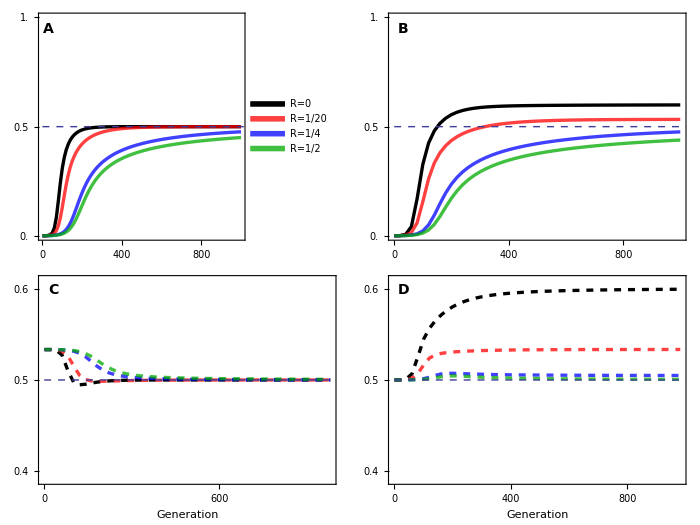

```mathematica
GraphicsGrid[{{plot1,plot2},{plot3,plot4}},
Spacings->-40,
Epilog->{
(*Text[Style["r=0.5, R=0.05",20],Scaled@{0.25,1.45}]*)
},
ImageSize->700
]

Export[plotdir<>"Combination_Turnover_Ratio.pdf",%];
```